# Constructing General Monte-Carlo Stochastic Differential Equation Solver

Khoa Tran - MATH 5111 - Professor Stojanovic -Mid-term Presentation
Source: Computational Financial Mathematics using Mathematica book.

This presentation will focus on building the general SDEsolver (i.e. the solver that can be used for both scalar and vector data). 
We will then apply the apply the solver to solve (i.e. show trajectories of) some example SDEs.

## SDEsolver for scalar (non-vector) data:

First, the (first-order) SDE:
	ⅆY(t) = f(t,y(t))ⅆt + σ(t,y(t))ⅆB(t)
Where f(t,y(t)) is a ordinary function, thus f(t,y(t))ⅆt is the deterministic part, while the second part σ(t,y(t))ⅆB(t) is the stochastic (random) part with σ(t,y(t)) is the function of standard deviation (or volatility in financial math) and ⅆB(t) as the realization of the Brownian motion for each ⅆt. 
We discretize the equation above (i.e. replace ⅆY(t) = y_(t+1)- y_t) and get:
	y_(t+1) = y_t + f(t,y(t))ⅆt + σ(t,y(t))ⅆB(t)
The Monte-Carlo SDEsolver for such equation is:

```mathematica
SDEsolver [f_,σ_,y0_,t0_,t1_,K_]:=Module[{dt,dB,G},dt=N[(t1-t0)/K];dB=Sqrt[dt] Table[Random[NormalDistribution[]],{K}];G[{t_,y_},db_]:={t+dt,y+f[t,y]dt+σ[t,y]db};FoldList[G,{t0,y0},dB]];
```

For demonstration, I’ll use our old homework:
	∫ⅇ^-t dB(t)
Here  ⅆY(t) = ⅇ^-tⅆB(t), assuming y(0) = 0, t_0=10, t_1=14, K = 400:

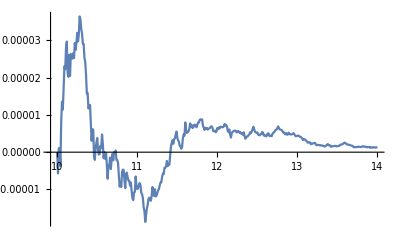

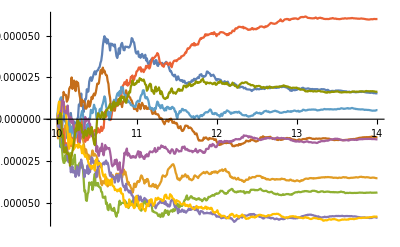

```mathematica
e[t_,x_] := Exp[-t];
pl1=ListPlot[SDE = SDEsolver[0 &,e,0,10,14,400],Joined->True,PlotRange->All]
MultiTraject = Table[SDE = SDEsolver[0 &,Exp[-#1]&,0,10,14,400],{10}];
ListPlot[MultiTraject,Joined->True,PlotRange->All]
```

Now we proceed to apply such solver into financial context. Assumption: the stock has the price S(0) = p, it grows with constant rate a (deterministic part of the model) and volatility σ. Thus we have the model:
	ⅆS(t) = aS(t)ⅆt + σS(t)ⅆB(t)

```mathematica
StockModel[a_,σ_,p_,T_] := SDEsolver[a #2&, σ#2&,p,0,T,1000]
```

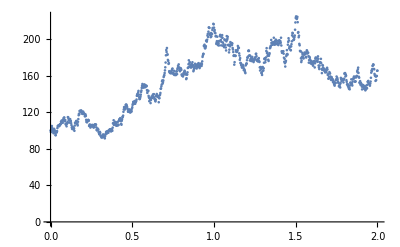

```mathematica
With[{T=2},price = StockModel[.3,.4,100,T];
ListPlot[price,PlotRange-> {0,Automatic}]];
```

## SDEsolver for m-dimensional data and General SDEsolver:

After seeing the application of such solver for modeling 1 stock price evolution, we attempt to expand the solver to be able to solve for multivariate SDEs:

```mathematica
SDEsolver2[f_,σ_,y0_,t0_,t1_,K_]:=Module[{n,dt,dB,G},n =Length[y0];dt=N[(t1-t0)/K];dB=Sqrt[dt] Table[Random[NormalDistribution[]],{K},{n}];FF[{t_,y_},db_]:={t+dt,y+b[t,y] dt+c[t,y].db};FoldList[FF,{t0,y0},dB]];
```

Having constructed the SDEsolver2, it would be useful for use to combine the 2 solvers into an if statement so the program can decide which solver to use based on whether the b function is a list or not.

```mathematica
GeneralSDEsolver[f_,σ_,y0_,t0_,t1_,K_] := If[Head[f[t0,y0]] === List, SDEsolver2[f,σ,y0,t0,t1,K], SDEsolver[f,σ,y0,t0,t1,K]]
```

To conclude the presentation, let’s apply the GeneralSDEsolver to model 2 stock price evolutions with multiple independent Brownian motions (sources of randomness)
	ⅆS(t) = S(t)aⅆt + S(t)σⅆB(t)
Where:

```mathematica
𝕡1=.2;𝕡2=.25;ρ=-.4;
```

```mathematica
b[t_,{y1_,y2_}]:={.1y1,-.15y2}
```

```mathematica
c[t_, {y1_,y2_}]:={y1 𝕡1,y2 𝕡2} {{1,0},{ρ,Sqrt[1-ρ^2]}}
```

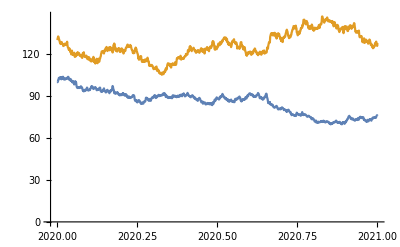

```mathematica
t0=2020;t1=2021;K=1000;dt=N[(t1-t0)/K];y0={100,130};
SDEx= GeneralSDEsolver[b,c,y0,t0,t1,K];
ListPlot[Table[{#[[1]],#[[2,k]]}&/@SDEx,{k,2}],Joined->True]
```